```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

## System Description

The system consists of two individual thermal transistors S1 and S2, connected in a Darlington pair configuration. The thermal flow between S1 and S2 is mediated via an intermediate energy divider mechanism. 
S1 - Connected to two thermal baths, B_HOT (collector), B_CNT (base) and emitter connected to the HIGH side of the energy divider
S2 - Connected to two thermal baths, B_HOT (collector), B_COL (emitter) and base connected to the LOW side of the energy divider

The thermal bath B_HOT is at a high temperature, while B_COL is at a low temperature. The temperature T_CNT of control terminal  B_CNT can be varied.
The energy divider mechanism receives and transmits energy to the two transistors.

Each transistor is modelled individually using the techniques developed for Optically Controlled Quantum Thermal Gate paper. However, we use a simplified 4×4 density matrix model instead of the previous 8×8 model. This is only valid under the conditions
	1. ω_L^S=ω_M^S=ω_R^S = 0
	2. ω_RL^S=0

The main reason for this is simplicity. Under a N-level energy divider and 8-level transistor model, we would have a 8×8×N = 64N dimensional vector space. This reduces to a 4×4×N = 16N level space under a 4-level transistor model.

## Energy divider parameters

N is the total number of quantum states in the intermediate system.
p is the number of jumps in the HIGH side.
q is the number of jumps in the LOW side

```mathematica
Ns=3;p=2;q=1;
```

The intermediate energy divider regulates the energy flow between the |3_T_1>↔|4_T_1> transition of the first transistor, and the |2_T_2><->|4_T_2> transition of the second transistor.
However, the|2_T_1>↔|1_T_1> transition of the first transistor, needs also be considered since they have the same transition frequency.

To properly match the energy levels in the HIGH and LOW sides, we need the conditions,
	1. ω_MR^T_1≃p ω_ED
	2. ω_MR^T_2-ω_LM^T_2 ≃q ω_ED
where ℏ ω_ED is the energy of the intermediate energy divider.

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

The system contains three subsystems T_1, T_2 and T_ED. 
T_1 and T_2 are thermal transistors modelled as 4-level systems. T_ED is a harmonic oscillator truncated at N levels.

#### Transistor Hamiltonian

Transistor Hamiltonian consists of two parts,
	1) The first part consists of the ultrastrong coupling between the three TLSs

```mathematica
HsT1Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=({{1/2 ℏ (Subscript[ωLM, 1]+Subscript[ωMR, 1]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, 1]-Subscript[ωMR, 1]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, 1]+Subscript[ωMR, 1]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, 1]+Subscript[ωMR, 1])}})[[veT1,hoT1]]Id[veED,hoED]Id[veT2,hoT2]
HsT2Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1]Id[veED,hoED]({{1/2 ℏ (Subscript[ωLM, 2]+Subscript[ωMR, 2]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, 2]-Subscript[ωMR, 2]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, 2]+Subscript[ωMR, 2]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, 2]+Subscript[ωMR, 2])}})[[veT2,hoT2]]
```

2) The second part consists of the field interactions with the external, tuned, electromagnetic field. The Hamiltonian below is given in its Schrodinger picture representation.

```mathematica
HlT1Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, 1])/2 ⅇ^(-ⅈ t (Subscript[ωLM, 1]-Subscript[ωMR, 1]))}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, 1])/2 ⅇ^(+ⅈ t (Subscript[ωLM, 1]-Subscript[ωMR, 1])), 0, 0}})[[veT1,hoT1]]Id[veED,hoED]Id[veT2,hoT2]
HlT2Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1]Id[veED,hoED]({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, 2])/2 ⅇ^(-ⅈ t (Subscript[ωLM, 2]-Subscript[ωMR, 2]))}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, 2])/2 ⅇ^(+ⅈ t (Subscript[ωLM, 2]-Subscript[ωMR, 2])), 0, 0}})[[veT2,hoT2]]
```

#### Energy divider Hamiltonian

```mathematica
Table[ℏ ωED(Ns-veED)veED,hoED,{veED,1,Ns},{hoED,1,Ns}]//MatrixForm
```

(2 ωED ℏ | 0 | 0
0 | ωED ℏ | 0
0 | 0 | 0)

```mathematica
HsEDSep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1](ℏ ωED(Ns-veED)veED,hoED)Id[veT2,hoT2]
```

### Forming the combined system Hamiltonian

The total number of combined system eigenstates are 4×N×4 = 16N.

In the matrix representation, we enumerate the energy levels as |(state of T_1) + (state of T_ED)+(state of T_2)>

the highest energy state |e,N,e> is given the first place, and the lowest energy state |g,0,g> is given the last space. 

For example,
|1>	= |1,N-1,1>
|2>	= |1,N-1,2>
|3>	= |1,N-1,3>
|4>	= |1,N-1,4>
|5> 	= |1,N-2,1>
|6> 	= |1,N-2,2>
....
|16N-3>	= |4,0,1>
|16N-2>	= |4,0,2>
|16N-1>	= |4,0,3>
|16N> 	= |4,0,4>

Eigenstate mapping function, maps overall state (1 to 16N) to subsystem T_1, T_ED, T_2 state,

```mathematica
EmapT1[i_]:=Quotient[i-1,4Ns]+1
EmapED[i_]:=Quotient[QuotientRemainder[i-1,4Ns][[2]],4]+1
EmapT2[i_]:=QuotientRemainder[i-1,4][[2]]+1
```

```mathematica
Table[EmapT1[i],{i,1,16Ns}]
Table[EmapED[i],{i,1,16Ns}]
Table[EmapT2[i],{i,1,16Ns}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4}

{1,1,1,1,2,2,2,2,3,3,3,3,1,1,1,1,2,2,2,2,3,3,3,3,1,1,1,1,2,2,2,2,3,3,3,3,1,1,1,1,2,2,2,2,3,3,3,3}

{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}

Matrix form of the three Hamiltonians

```mathematica
HsT1[ve_,ho_]:=HsT1Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HsED[ve_,ho_]:=HsEDSep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HsT2[ve_,ho_]:=HsT2Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]

HlT1[ve_,ho_]:=HlT1Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HlT2[ve_,ho_]:=HlT2Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space (We consider the field interaction (Ĥ)_(field-sys)^S as a perturbation. Hence it is not included here, but in the Hsys1Matrix.

```mathematica
Hsys0Matrix = Table[HsT1[ve,ho]+HsED[ve,ho]+HsT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Diagonal[Hsys0Matrix]//MatrixForm
```

(2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2))

## Interaction Hamiltonian between the subsystems

The interactions between the subsystems are considered WEAK enough such that the local master equation approach is justified.
This effectively means that the subsystem interactions should not significantly change the energy levels of the non-interacting, subsystem Hamiltonians.

The energy levels of the individual components are specially tuned in our model. 
	1. First of all, there are no direct interactions between T_1 and T_2.
	2. The energy levels are prepared so that
		ω_MR^T_1≃p ω_ED
		ω_MR^T_2-ω_LM^T_2 ≃q ω_ED
	3. Therefore the interactions are such that
		a) T_1 jumps up from |3_T_1> to |4_T_1> (or |2_T_1> to |1_T_1> ) while the HO jumps down p steps from |(m+p)_T_ED> to |m_T_ED> (and vice versa).
		b) T_2 jumps up from |2_T_2> to |4_T_2> while the HO jumps down q steps from |(m+q)_T_ED> to |m_T_ED> (and vice versa).
	3. The interaction strengths between subsystems are given by γ_T_1[m] and γ_T_2[m] with m enumerating the different start (or end) state of the HO.

First define some necessary matrices

```mathematica
OneMatrix[ve_,ho_,n_]:=Table[ve,i ho,j,{i,1,n},{j,1,n}]
OneMatrix[Ns-0,Ns-(0+p),Ns]//MatrixForm
{OneMatrix[Ns-0,Ns-(0+q),Ns]//MatrixForm,
OneMatrix[Ns-1,Ns-(1+q),Ns]//MatrixForm}
```

(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0)

{(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0),(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0)}

Considering the above Hamiltonian, we write the interaction between T_1 and T_ED as,

```mathematica
HintT1andED[ve_,ho_]:=(∑_(m=0)^(Ns-1-p) ℏ γT1[m]KroneckerProduct[(KroneckerProduct[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}}),OneMatrix[Ns-m,Ns-(m+p),Ns]]+KroneckerProduct[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),OneMatrix[Ns-(m+p),Ns-m,Ns]]),IdentityMatrix[4]])[[ve,ho]]
```

Similarly, we write the interaction between T_ED and T_2 as,

```mathematica
HintEDandT2[ve_,ho_]:=(∑_(m=0)^(Ns-1-q) ℏ γT2[m]KroneckerProduct[IdentityMatrix[4],(KroneckerProduct[OneMatrix[Ns-m,Ns-(m+q),Ns],({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}})]+KroneckerProduct[OneMatrix[Ns-(m+q),Ns-m,Ns],({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})])])[[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix = Table[HintT1andED[ve,ho]+HintEDandT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Hsys2Matrix = Table[HlT1[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Hsys3Matrix = Table[HlT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
{MatrixForm[Hsys1Matrix],MatrixForm[Hsys2Matrix],,MatrixForm[Hsys3Matrix]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),Null,(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0)}

## Combined system Hamiltonian

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix+Hsys2Matrix+Hsys3Matrix;
MatrixForm[HsysMatrix]
```

(2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2))

## Density Matrix

In the combined system, the density matrix is 12×12.

```mathematica
ρMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,16Ns},{ho,1,16Ns}]
```

```mathematica
MatrixForm[ρMatrix[t]]
```

(1)
 |  |  |  |

## System-bath interactions

The inter-subsystem interaction Hamiltonian is supposed to be in the weak regime. The energy eigensystems of the individual subsystems are minimally affected by this interaction.
This means that it is enough to model the thermal interactions in the bare eigensystem of only the individual transistor Hamiltonians.

### Thermal interactions of individual transistors

In the simplified individual transistor model, each bath has two Lindblad operators

```mathematica
Subscript[LinOps, S_,P_][i_]:=({{({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})}})[[P,i]]
Subscript[ωLinOps, S_,P_][i_]:=({{-Subscript[ωLM, S], -Subscript[ωLM, S]}, {-Subscript[ωLM, S]-Subscript[ωMR, S], -Subscript[ωLM, S]+Subscript[ωMR, S]}, {-Subscript[ωMR, S], Subscript[ωMR, S]}})[[P,i]]
```

### Interactions of the hot bath B_HOT

B_HOT is connected to the collectors of both T_1 and T_2. Hence, we need to extract the S=1, P=1 and S=2, P=1 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT1BHOT[i_]:=KroneckerProduct[Subscript[LinOps, 1,1][i],KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[4]]]
ωT1BHOT[i_]:=Subscript[ωLinOps, 1,1][i]
AMatrixT2BHOT[i_]:=KroneckerProduct[IdentityMatrix[4],KroneckerProduct[IdentityMatrix[Ns],Subscript[LinOps, 2,1][i]]]
ωT2BHOT[i_]:=Subscript[ωLinOps, 2,1][i]
```

```mathematica
Table[MatrixForm[AMatrixT1BHOT[i]],{i,1,2}];
Table[MatrixForm[AMatrixT2BHOT[i]],{i,1,2}];
Table[MatrixForm[ωT1BHOT[i]],{i,1,2}]
Table[MatrixForm[ωT2BHOT[i]],{i,1,2}]
```

{-ωLM_1,-ωLM_1}

{-ωLM_2,-ωLM_2}

### Interactions of the control bath B_CNT

B_CNT is connected to the base of T_1. Hence, we need to extract the S=1, P=2 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT1BCNT[i_]:=KroneckerProduct[Subscript[LinOps, 1,2][i],KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[4]]]
ωT1BCNT[i_]:=Subscript[ωLinOps, 1,2][i]
```

```mathematica
Table[MatrixForm[AMatrixT1BCNT[i]],{i,1,2}];
Table[MatrixForm[ωT1BCNT[i]],{i,1,2}]
```

{-ωLM_1-ωMR_1,-ωLM_1+ωMR_1}

### Interactions of the cold bath B_COL

B_COL is connected to the emitter of T_2. Hence, we need to extract the S=2, P=3 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT2BCOL[i_]:=KroneckerProduct[IdentityMatrix[4],KroneckerProduct[IdentityMatrix[Ns],Subscript[LinOps, 2,3][i]]]
ωT2BCOL[i_]:=Subscript[ωLinOps, 2,3][i]
```

```mathematica
Table[MatrixForm[AMatrixT2BCOL[i]],{i,1,2}];
Table[MatrixForm[ωT2BCOL[i]],{i,1,2}]
```

{-ωMR_2,ωMR_2}

### Lindblad terms of the master equation

```mathematica
LinTerm[ρ_,A_,J_,NBE_,ω_]:=∑_(i=1)^2 (J[ω[i]](1+NBE[ω[i]])(A[i].ρ.A[i]†-1/2(A[i]†.A[i].ρ+ρ.A[i]†.A[i]))+J[ω[i]]NBE[ω[i]](A[i]†.ρ.A[i]-1/2(A[i].A[i]†.ρ+ρ.A[i].A[i]†)))
```

```mathematica
LinMatrixT1BHOT[ρ_]:=LinMatrixT1BHOT[ρ]=LinTerm[ρ,AMatrixT1BHOT,Subscript[J, 1],Subscript[NBE, 1],ωT1BHOT]
LinMatrixT2BHOT[ρ_]:=LinMatrixT2BHOT[ρ]=LinTerm[ρ,AMatrixT2BHOT,Subscript[J, 1],Subscript[NBE, 1],ωT2BHOT]
LinMatrixT1BCNT[ρ_]:=LinMatrixT1BCNT[ρ]=LinTerm[ρ,AMatrixT1BCNT,Subscript[J, 2],Subscript[NBE, 2],ωT1BCNT]
LinMatrixT2BCOL[ρ_]:=LinMatrixT2BCOL[ρ]=LinTerm[ρ,AMatrixT2BCOL,Subscript[J, 3],Subscript[NBE, 3],ωT2BCOL]
```

```mathematica
MatrixForm[LinMatrixT1BHOT[ρMatrix[t]]]
MatrixForm[LinMatrixT2BHOT[ρMatrix[t]]]
MatrixForm[LinMatrixT1BCNT[ρMatrix[t]]]
MatrixForm[LinMatrixT2BCOL[ρMatrix[t]]]
```

(1)
 |  |  |  |

(1)
 |  |  |  |

(1)
 |  |  |  |

«1 more identical outputs»

## Defining the interaction picture

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
Hsys2INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys2Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
Hsys3INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys3Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
MatrixForm[Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0)

## Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHSengdiv=-ⅈ/ℏ(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix);
Subscript[RHSfield, 1]=-ⅈ/ℏ(Hsys2INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys2INTMatrix);
Subscript[RHSfield, 2]=-ⅈ/ℏ(Hsys3INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys3INTMatrix);
```

```mathematica
RHS=RHSengdiv+Subscript[RHSfield, 1]+Subscript[RHSfield, 2]+LinMatrixT1BHOT[ρMatrix[t]]+LinMatrixT2BHOT[ρMatrix[t]]+LinMatrixT1BCNT[ρMatrix[t]]+LinMatrixT2BCOL[ρMatrix[t]];
RHS=Collect[RHS,Flatten[{Table[{Subscript[J, P][ω_]},{P,1,3}],Subscript[Ω, 1],Subscript[Ω, 2],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]]]&];
```

Left hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(1)
 |  |  |  |

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,16Ns},{j,1,16Ns}]]]/.Rule->Equal];
```

```mathematica
sol=ApplySides[Collect[Expand[#],Flatten[{Table[{Subscript[J, P][ω_]},{P,1,3}],Subscript[Ω, 1],Subscript[Ω, 2],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]]]&]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;(16Ns+1)]];
soloffdiag=Delete[sol,Table[{1+(16Ns+1)i},{i,0,(16Ns-1)}]];
MatrixForm[soldiag]
MatrixForm[soloffdiag];
```

(1)
 |  |  |  |

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

We can define four thermal flows into the system, two from B_H and one each from B_N and B_C. Similarly, two energy flows from the field to T_1 and T_2 can also be defined.

```mathematica
Subscript[EngyFlowIn, 1,1][ρ_]:=Subscript[EngyFlowIn, 1,1][ρ]=Tr[LinMatrixT1BHOT[ρ].Hsys0Matrix]
Subscript[EngyFlowIn, 1,2][ρ_]:=Subscript[EngyFlowIn, 1,2][ρ]=Tr[LinMatrixT2BHOT[ρ].Hsys0Matrix]
Subscript[EngyFlowIn, 2][ρ_]:=Subscript[EngyFlowIn, 2][ρ]=Tr[LinMatrixT1BCNT[ρ].Hsys0Matrix]
Subscript[EngyFlowIn, 3][ρ_]:=Subscript[EngyFlowIn, 3][ρ]=Tr[LinMatrixT2BCOL[ρ].Hsys0Matrix]
Subscript[EngyFlowIn, 4,1][ρ_]:=Subscript[EngyFlowIn, 4,1][ρ]=Tr[Subscript[RHSfield, 1].Hsys0Matrix]
Subscript[EngyFlowIn, 4,2][ρ_]:=Subscript[EngyFlowIn, 4,2][ρ]=Tr[Subscript[RHSfield, 2].Hsys0Matrix]
```

```mathematica
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&]

Subscript[EngyFlowIn, 2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&]

Subscript[EngyFlowIn, 3][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&]

Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&]
```

-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(1,1)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(2,2)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(3,3)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(4,4)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(5,5)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(6,6)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(7,7)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(8,8)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(9,9)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(10,10)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(11,11)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(12,12)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(13,13)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(14,14)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(15,15)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(16,16)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(17,17)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(18,18)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(19,19)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(20,20)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(21,21)[t]-ℏ (ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(22,22)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(23,23)[t]+ℏ (-ωLM_1 J_1[-ωLM_1] NBE_1[-ωLM_1]+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(24,24)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(25,25)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(26,26)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(27,27)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(28,28)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(29,29)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(30,30)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(31,31)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(32,32)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(33,33)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(34,34)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(35,35)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(36,36)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(37,37)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(38,38)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(39,39)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(40,40)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(41,41)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(42,42)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(43,43)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(44,44)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(45,45)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])-ωLM_2 J_1[-ωLM_2] NBE_1[-ωLM_2]) ρ_(46,46)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(47,47)[t]+ℏ (ωLM_1 J_1[-ωLM_1] (1+NBE_1[-ωLM_1])+ωLM_2 J_1[-ωLM_2] (1+NBE_1[-ωLM_2])) ρ_(48,48)[t]

-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(1,1)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(2,2)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(3,3)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(4,4)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(5,5)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(6,6)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(7,7)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(8,8)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(9,9)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(10,10)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(11,11)[t]-ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] NBE_2[-ωLM_1-ωMR_1] ρ_(12,12)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(13,13)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(14,14)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(15,15)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(16,16)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(17,17)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(18,18)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(19,19)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(20,20)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(21,21)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(22,22)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(23,23)[t]+ℏ (-ωLM_1+ωMR_1) J_2[-ωLM_1+ωMR_1] NBE_2[-ωLM_1+ωMR_1] ρ_(24,24)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(25,25)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(26,26)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(27,27)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(28,28)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(29,29)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(30,30)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(31,31)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(32,32)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(33,33)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(34,34)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(35,35)[t]+ℏ (ωLM_1+ωMR_1) J_2[-ωLM_1-ωMR_1] (1+NBE_2[-ωLM_1-ωMR_1]) ρ_(36,36)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(37,37)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(38,38)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(39,39)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(40,40)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(41,41)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(42,42)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(43,43)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(44,44)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(45,45)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(46,46)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(47,47)[t]+ℏ (ωLM_1-ωMR_1) J_2[-ωLM_1+ωMR_1] (1+NBE_2[-ωLM_1+ωMR_1]) ρ_(48,48)[t]

-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(1,1)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(2,2)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(3,3)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(4,4)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(5,5)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(6,6)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(7,7)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(8,8)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(9,9)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(10,10)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(11,11)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(12,12)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(13,13)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(14,14)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(15,15)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(16,16)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(17,17)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(18,18)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(19,19)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(20,20)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(21,21)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(22,22)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(23,23)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(24,24)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(25,25)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(26,26)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(27,27)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(28,28)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(29,29)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(30,30)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(31,31)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(32,32)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(33,33)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(34,34)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(35,35)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(36,36)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(37,37)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(38,38)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(39,39)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(40,40)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(41,41)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(42,42)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(43,43)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(44,44)[t]-ℏ ωMR_2 J_3[-ωMR_2] NBE_3[-ωMR_2] ρ_(45,45)[t]+ℏ ωMR_2 J_3[-ωMR_2] (1+NBE_3[-ωMR_2]) ρ_(46,46)[t]+ℏ ωMR_2 J_3[ωMR_2] NBE_3[ωMR_2] ρ_(47,47)[t]-ℏ ωMR_2 J_3[ωMR_2] (1+NBE_3[ωMR_2]) ρ_(48,48)[t]

-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(2,4)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(4,2)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(6,8)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(8,6)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(10,12)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(12,10)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(13,37)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(14,16)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(14,38)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(15,39)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(16,14)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(16,40)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(17,41)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(18,20)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(18,42)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(19,43)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(20,18)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(20,44)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(21,45)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(22,24)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(22,46)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(23,47)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(24,22)[t]-1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(24,48)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(26,28)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(28,26)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(30,32)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(32,30)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(34,36)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(36,34)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(37,13)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(38,14)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(38,40)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(39,15)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(40,16)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(40,38)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(41,17)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(42,18)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(42,44)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(43,19)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(44,20)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(44,42)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(45,21)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(46,22)[t]-1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(46,48)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(47,23)[t]+1/2 ⅈ ℏ Ω_1 (ωLM_1-ωMR_1) ρ_(48,24)[t]+1/2 ⅈ ℏ Ω_2 (ωLM_2-ωMR_2) ρ_(48,46)[t]

## On unit conversions

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

## Density matrix, transition rate and energy flow evolution with time

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2 ωconv,
ωED->0.4ωconv,
Subscript[Ω, 1]->0.000ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.10 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2 ωconv,
ωED->0.4ωconv,
Subscript[Ω, 1]->0.000ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2 ωconv,
ωED->0.4ωconv,
Subscript[Ω, 1]->0.007ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
γassum={γT1[i_]->0.0ωconv,γT2[i_]->0.0ωconv};
```

```mathematica
γassum={γT1[i_]->0.015ωconv,γT2[i_]->0.015ωconv};
```

```mathematica
γassum={γT1[i_]->0.030ωconv,γT2[i_]->0.030ωconv};
```

Energy levels for this configuration

```mathematica
{MatrixForm[Hsys0Matrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]]};
```

Numerical solution of the dynamics, with the initial condition of ground state.

```mathematica
initρMatrix =Table[i,j i,35 1,{i,1,16Ns},{j,1,16Ns}];
```

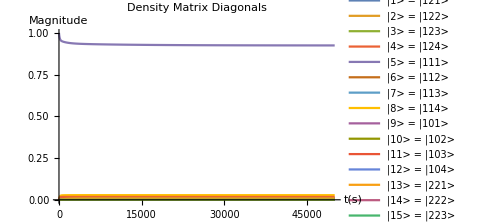
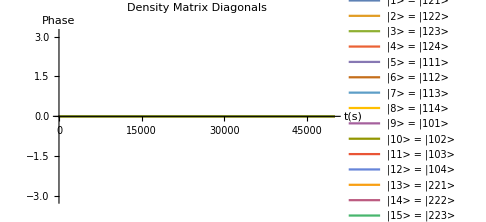

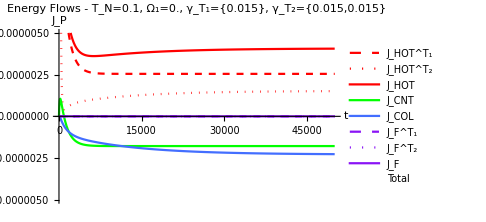

```mathematica
tmax=(50000/ωconv)//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,16Ns},{j,1,16Ns}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,0,tmax}
];

plot1=Flatten[{Table[Abs[Subscript[ρ, i,i][t]],{i,1,16Ns}]}/.dynamics];
plot2=Flatten[{Table[Arg[Subscript[ρ, i,i][t]],{i,1,16Ns}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0,1},
	AxesLabel->{Style["t(s)"],Style["Magnitude"]}, 
	PlotLegends->Table[StringForm["|``> = |``````>",i,EmapT1[i],Ns-EmapED[i],EmapT2[i]],{i,1,16Ns}]
],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {-π,π},
	AxesLabel->{Style["t(s)"],Style["Phase"]}, 
	PlotLegends->Table[StringForm["|``> = |``````>",i,EmapT1[i],Ns-EmapED[i],EmapT2[i]],{i,1,16Ns}]
]}

Flatten[{
Subscript[EngyFlowIn, 1,1][ρMatrix[t]],Subscript[EngyFlowIn, 1,2][ρMatrix[t]],Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],
Subscript[EngyFlowIn, 4,1][ρMatrix[t]],Subscript[EngyFlowIn, 4,2][ρMatrix[t]],Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]],
Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]+Subscript[EngyFlowIn, 3][ρMatrix[t]]+Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]]}//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style[StringForm["Energy Flows - T_N=``, Ω_1=``, 
γ_T_1=``, γ_T_2=``",Subscript[T, 2],Subscript[Ω, 1],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]]/.Flatten[{γassum,Tassum}]],
	PlotRange->{Automatic, {-0.5 10^-3 Econv Subscript[κ, 1]/.Tassum,0.5 10^-3 Econv Subscript[κ, 1]/.Tassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"J_HOT^T_1","J_HOT^T_2","J_HOT","J_CNT","J_COL","J_F^T_1","J_F^T_2","J_F","Total"},
	PlotStyle->{{Red,Dashed},{Red,Dotted},Red,Green,BlueC,{PurpleC,Dashed},{PurpleC,Dotted},PurpleC,{White,Dashed}}]
```

## Numerically obtaining the approximate steady-state

Because ParallelTable doesn’t work properly with EngyFlowIn_P[ρ], we need to redefine them

```mathematica
EngyFlowInHT1=Subscript[EngyFlowIn, 1,1][ρMatrix[t]];
EngyFlowInHT2=Subscript[EngyFlowIn, 1,2][ρMatrix[t]];
EngyFlowInN=Subscript[EngyFlowIn, 2][ρMatrix[t]];
EngyFlowInC=Subscript[EngyFlowIn, 3][ρMatrix[t]];
EngyFlowInFT1=Subscript[EngyFlowIn, 4,1][ρMatrix[t]];
EngyFlowInFT2=Subscript[EngyFlowIn, 4,2][ρMatrix[t]];
```

```mathematica
varFunc[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,tmax_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NDSolve[
Flatten[{temp1,Table[Subscript[ρ, i,j][0]==i,j i,35 1,{i,1,16Ns},{j,1,16Ns}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,0,tmax}];
temp3=Table[Subscript[ρ, i,j][tmax],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i][tmax],{i,1,16Ns}]/.temp2]],
Re[Flatten[{
EngyFlowInHT1,EngyFlowInHT2,EngyFlowInHT1+EngyFlowInHT2,EngyFlowInN,EngyFlowInC,
EngyFlowInFT1,EngyFlowInFT2,EngyFlowInFT1+EngyFlowInFT2,
EngyFlowInHT1+EngyFlowInHT2+EngyFlowInN+EngyFlowInC+EngyFlowInFT1+EngyFlowInFT2}//.Flatten[{t->tmax,temp0}]/.temp2]]
}
]
```

```mathematica
varFunc[0.2,0.10,0.02,0.01,0.01,0.01,0.7,0.8,0.8,1.2,0.4,0.0,0.0,{0.015},{0.015,0.015},50000,unitassum]
```

{{2.04786×10^-14,7.126×10^-9,8.24383×10^-7,1.39101×10^-12,4.25694×10^-11,8.03972×10^-9,1.08468×10^-6,5.65175×10^-9,3.3504×10^-11,1.20278×10^-6,0.0000865344,5.57606×10^-9,5.7219×10^-11,2.5739×10^-6,0.000261349,4.95399×10^-9,1.57971×10^-8,2.81072×10^-6,0.000333128,2.08783×10^-6,1.62054×10^-8,0.000500679,0.0276289,2.20348×10^-6,3.92375×10^-9,0.000114133,0.00882424,4.49796×10^-7,5.64046×10^-7,0.0000944819,0.0111299,0.000076199,5.49734×10^-7,0.0169321,0.924809,0.0000742333,2.94559×10^-12,7.31548×10^-7,0.0000841451,2.09102×10^-10,4.39241×10^-9,8.36875×10^-7,0.000110471,5.82269×10^-7,2.68269×10^-9,0.000107958,0.00881533,4.1262×10^-7},{2.54428×10^-6,1.51044×10^-6,4.05471×10^-6,-1.78161×10^-6,-2.26572×10^-6,0.,0.,0.,7.37593×10^-9}}

## Energy flow characteristics for different system parameters

### Energy flow under different control temperatures

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping the γs constant,

```mathematica
PlotEngyFlowsWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1s_,Ω2s_,γT1s_,γT2s_,Tcntmin_,Tcntmax_,Tres_,tmax_,legends_,title_]:=Module[{tempx,tempy,temp},
tempx=Table[Tcnt/Thot,{Tcnt,Tcntmin,Tcntmax,Tres},{i,1,9}];
tempy=10^6 ParallelTable[varFunc[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1s,Ω2s,γT1s,γT2s,tmax,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,i]]}],{i,1,9}];
ListPlot[temp,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{-5,6}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
PlotStyle->{{Red,Dashed},{Red,Dotted},{Red},{Green},{BlueC},{PurpleC,Dashed},{PurpleC,Dotted},PurpleC,{White,Dashed}},
PlotLegends->legends &&{
Style["J_H^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["Total",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

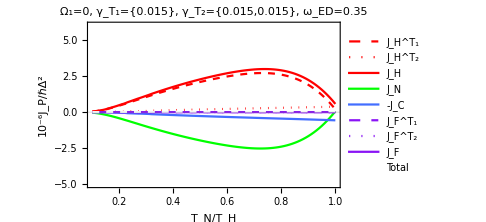
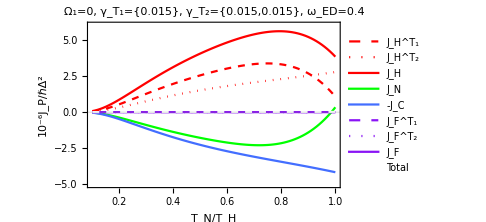
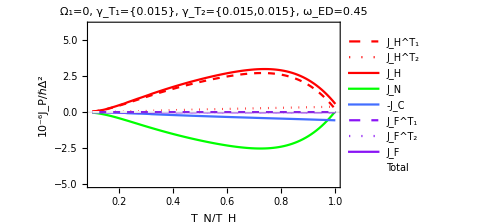

```mathematica
{
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,tmaxs},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.01;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.35ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,tmaxs,True,StringForm["Ω_1=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Ω1,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,tmaxs},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.01;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.4ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,tmaxs,True,StringForm["Ω_1=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Ω1,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,tmaxs},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.01;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.45ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,tmaxs,True,StringForm["Ω_1=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Ω1,γT1s,γT2s,ωEDs]]
]
}
```

### Energy flow under different field strengths

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping the γs constant,

```mathematica
PlotEngyFlowsWithΩ1[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω2s_,γT1s_,γT2s_,Ω1min_,Ω1max_,Ωres_,tmax_,legends_,title_]:=Module[{tempx,tempy,temp},
tempx=Table[Ω1/(κhot ωconv),{Ω1,Ω1min,Ω1max,Ωres},{i,1,9}];
tempy=10^6 ParallelTable[varFunc[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2s,γT1s,γT2s,tmax,unitassum],{Ω1,Ω1min,Ω1max,Ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,i]]}],{i,1,9}];
ListPlot[temp,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{-5,6}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
PlotStyle->{{Red,Dashed},{Red,Dotted},{Red},{Green},{BlueC},{PurpleC,Dashed},{PurpleC,Dotted},PurpleC,{White,Dashed}},
PlotLegends->legends &&{
Style["J_H^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["Total",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

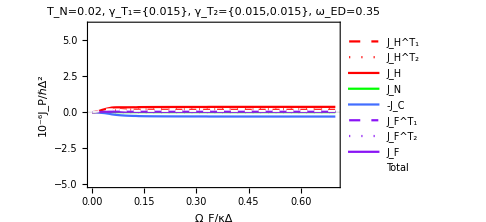
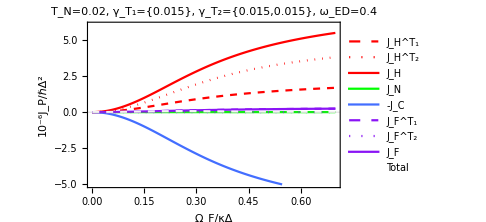
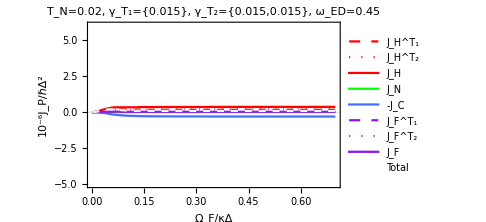

```mathematica
{
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.35ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.40ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.45ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
]
}
```

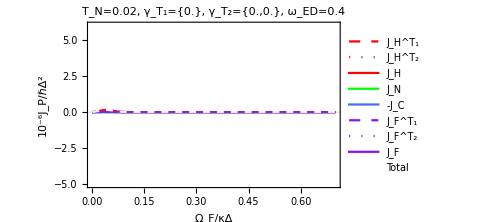
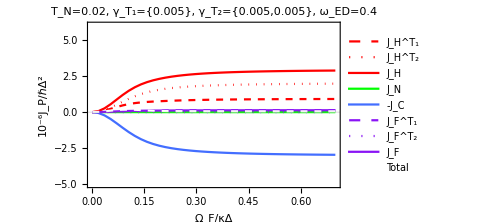
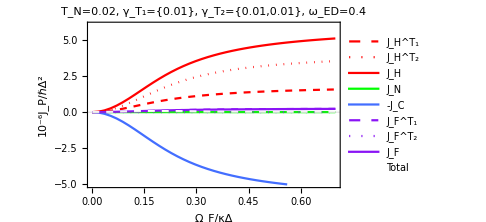
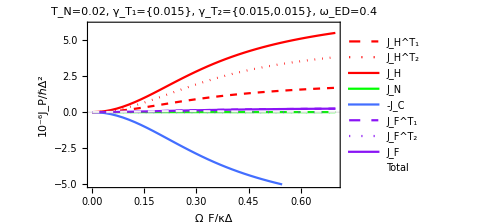
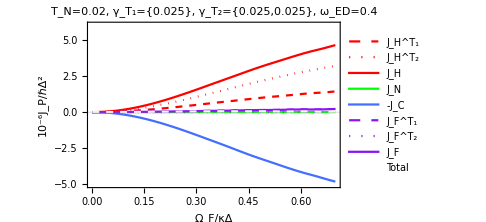

```mathematica
{
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.40ωconv;
γT1s={0.00ωconv};
γT2s={0.00ωconv,0.00ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.40ωconv;
γT1s={0.005ωconv};
γT2s={0.005ωconv,0.005ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.40ωconv;
γT1s={0.010ωconv};
γT2s={0.010ωconv,0.010ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.40ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=0.8ωconv;ωMR2=1.2ωconv;ωEDs=0.40ωconv;
γT1s={0.025ωconv};
γT2s={0.025ωconv,0.025ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,tmaxs,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
]
}
```